```mathematica
InverseNull[n_]:=First[Select[realyNullAtomKeys,allGraphs[#,"colofourrealnull"]==n&]]
```

```mathematica
Select[Table[Simplify[ allGraphs[k,"comp"][allGraphs[k,"colofourrealnull"],0]],{k,Keys[allGraphs]}],Length[ListofVars[#]]==2&];
```

```mathematica
lattice=Map[InverseNull[#[[1]]]->InverseNull[#[[2]]]&, Select[Table[Simplify[ allGraphs[k,"comp"][allGraphs[k,"colofourrealnull"],0]],{k,Keys[allGraphs]}],Length[ListofVars[#]]==2&]];
```

```mathematica
direct=Select[
Flatten[
Table[
Table[
{
If[ToString[allGraphs[c[[1]],"comp"]]=="Greater",
 k->c[[2]]
];
If[ToString[allGraphs[c[[2]],"comp"]]=="Greater",
k->c[[1]]
]
}
,{c,allGraphs[k,"children"]}
]
,
{k,{19683,39366}}
]],
ToString[#]≠"Null"&];
```

```mathematica
direct2=Select[
Flatten[
Table[
Table[
{
If[ToString[allGraphs[c[[1]],"comp"]]=="GreaterEqual",
 k->c[[2]]
];
If[ToString[allGraphs[c[[2]],"comp"]]=="GreaterEqual",
k->c[[1]]
]
}
,{c,allGraphs[k,"children"]}
]
,
{k,Keys[allGraphs]}
]],
ToString[#]≠"Null"&];
```

```mathematica
allGraphs[0,"children"]
```

{{19683,39366},{6561,13122},{2187,4374},{729,1458},{243,486},{81,162},{27,54},{9,18},{3,6},{1,2}}

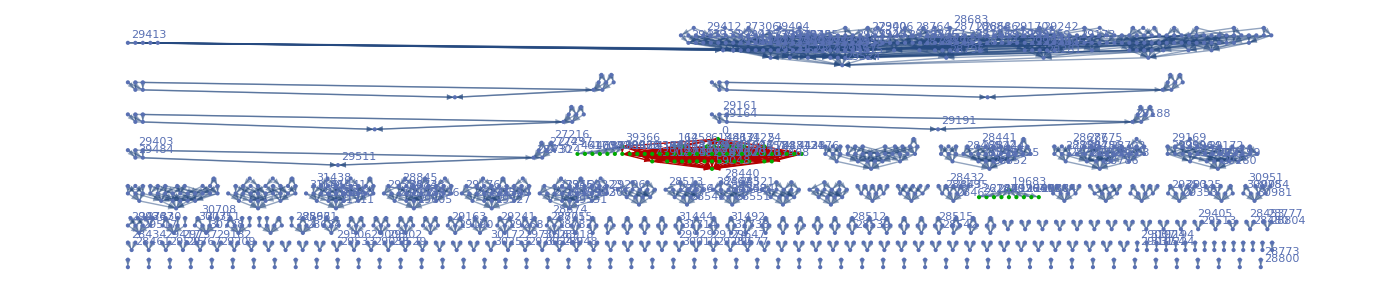

```mathematica
Graph[DeleteDuplicates[Join[lattice,direct,direct2]], 
VertexLabels->"Name",
VertexStyle->Table[k->ColourForKey[allGraphs,k],{k,DeleteDuplicates[Flatten[Map[{#[[1]],#[[2]]}&,Join[lattice,direct]]]]}],
GraphHighlight->lattice,
GraphLayout->{"LayeredDigraphEmbedding","Orientation"->Top},
ImageSize->1400]
```

```mathematica
Eigenvectors[N[KirchhoffMatrix[%1334]]]
```

Eigenvectors::arh: Because finding 1895 out of the 1895 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigenvectors.

{1}
 |  |  |  |

```mathematica
$HistoryLength=5
```

5

```mathematica
allGraphs[29608,"graph"]
```

-Graphics-

```mathematica
Map[{Style[#[[1]],If[MemberQ[realyNullAtomKeys,#[[2]]],Bold,Plain],If[MemberQ[atomKeys,#[[2]]],Underlined,Plain],ColourForKey[allGraphs,#[[2]]] ],allGraphs[#[[2]],"graph"]}&, Take[Table[{allGraphs[k,"colofour"]/.demoValues,k},{k,Keys[allGraphs]}]//Sort,100]]
```

{{0,-Graphics-},{16,-Graphics-},{25,-Graphics-},{27,-Graphics-},{27,-Graphics-},{28,-Graphics-},{28,-Graphics-},{30,-Graphics-},{30,-Graphics-},{30,-Graphics-},{33,-Graphics-},{35,-Graphics-},{38,-Graphics-},{40,-Graphics-},{41,-Graphics-},{41,-Graphics-},{41,-Graphics-},{41,-Graphics-},{43,-Graphics-},{44,-Graphics-},{46,-Graphics-},{52,-Graphics-},{52,-Graphics-},{52,-Graphics-},{53,-Graphics-},{53,-Graphics-},{53,-Graphics-},{54,-Graphics-},{54,-Graphics-},{58,-Graphics-},{58,-Graphics-},{58,-Graphics-},{62,-Graphics-},{63,-Graphics-},{63,-Graphics-},{63,-Graphics-},{63,-Graphics-},{64,-Graphics-},{66,-Graphics-},{66,-Graphics-},{68,-Graphics-},{68,-Graphics-},{68,-Graphics-},{68,-Graphics-},{68,-Graphics-},{68,-Graphics-},{69,-Graphics-},{70,-Graphics-},{71,-Graphics-},{71,-Graphics-},{71,-Graphics-},{72,-Graphics-},{72,-Graphics-},{72,-Graphics-},{73,-Graphics-},{74,-Graphics-},{74,-Graphics-},{74,-Graphics-},{74,-Graphics-},{74,-Graphics-},{74,-Graphics-},{76,-Graphics-},{78,-Graphics-},{78,-Graphics-},{78,-Graphics-},{79,-Graphics-},{79,-Graphics-},{79,-Graphics-},{79,-Graphics-},{80,-Graphics-},{81,-Graphics-},{82,-Graphics-},{82,-Graphics-},{82,-Graphics-},{83,-Graphics-},{83,-Graphics-},{84,-Graphics-},{85,-Graphics-},{86,-Graphics-},{86,-Graphics-},{87,-Graphics-},{87,-Graphics-},{88,-Graphics-},{88,-Graphics-},{90,-Graphics-},{90,-Graphics-},{93,-Graphics-},{93,-Graphics-},{93,-Graphics-},{94,-Graphics-},{95,-Graphics-},{96,-Graphics-},{96,-Graphics-},{96,-Graphics-},{96,-Graphics-},{98,-Graphics-},{98,-Graphics-},{98,-Graphics-},{99,-Graphics-},{99,-Graphics-}}

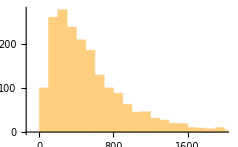

```mathematica
Histogram[Table[allGraphs[k,"colofour"]/.demoValues,{k,Keys[allGraphs]}]]
```

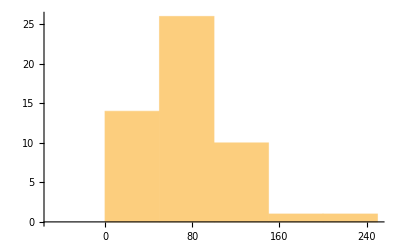

```mathematica
Histogram[Table[allGraphs[k,"colofour"]/.demoValues,{k,atomKeys}]]
```

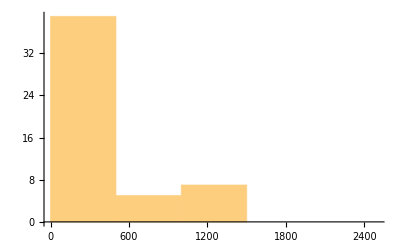

```mathematica
Histogram[Table[allGraphs[k,"colofour"]/.demoValues,{k,realyNullAtomKeys}]]
```

```mathematica
Table[allGraphs[k,"parents"],{k,{quad1Key,quad2Key,quad3Key,quad4Key,quad5Key}}]
```

{{36084,36058,36004,35353,35353,33889,33889,22963,22960,22954,22951,22720,22717,22711,22708,22234,22225,21991,21982,20776,20773,20533,20530,20047,19804,16159,16159,3280,3277,3271,3268,2551,2542,1093,1090,364},{29602,29577,29577,29442,29443,29433,29434,29416,29407,29353,29353,29199,29200,29173,28876,27255,27256,27246,27247,27229,27220,27012,27013,26986,23044,9759,9760,9750,9751,9733,9724,9516,9517,9490,7735,7735},{29520,29521,29517,29517,29512,29493,29494,29485,29446,29277,29278,29269,29257,29257,28791,28792,28783,28764,28765,28756,28548,28549,28540,27340,22959,22960,22951,22932,22933,22924,22716,22717,22708,22237,22237,9844},{31708,31684,31468,30981,30981,27336,27337,27327,27328,27255,27256,27246,27247,26608,26599,26527,26518,25141,25141,20775,20776,20694,20695,20047,19966,11947,11947,7653,7654,7644,7645,6925,6916,1092,1093,364},{29542,29493,29496,29497,29494,29469,29469,29416,29413,29305,29305,29253,29254,29173,28764,28767,28768,28765,28687,28684,28524,28525,28444,27364,22990,9810,9813,9814,9811,9733,9730,9570,9571,9490,9139,9139}}

```mathematica
ProduceEq[parent_,child_]:=Block[{other},
Table[
other=First[Select[c,#≠child&]];
allGraphs[parent,"colofour"]==allGraphs[other,"colofour"],
{c, Select[allGraphs[parent,"children"],MemberQ[#,child]&]}
]
]
```

```mathematica
Table[
Table[
ProduceEq[p,k],
{p,
allGraphs[k,"parents"]}
],{k,{alfa1Key,beta1Key,gamma1Key,delta1Key,epsilon1Key}}]//Flatten//DeleteDuplicates
```

{v13x245+v13x24x5==v13x245,v13x24x5+v13x2x45+v13x2x4x5==v13x2x45+v13x2x4x5,v13x24x5+v13x2x4x5==v13x2x4x5,v13x24x5+v13x25x4+v13x2x4x5==v13x25x4+v13x2x4x5,v135x24+v13x24x5==v135x24,v134x2x5+v13x24x5+v13x2x45+v13x2x4x5==v134x2x5+v13x2x45+v13x2x4x5,v134x2x5+v13x24x5+v13x2x4x5==v134x2x5+v13x2x4x5,v134x25+v134x2x5+v13x24x5+v13x25x4+v13x2x4x5==v134x25+v134x2x5+v13x25x4+v13x2x4x5,v13x24x5+v1x24x35+v1x24x3x5==v1x24x35+v1x24x3x5,v13x24x5+v1x24x3x5==v1x24x3x5,v13x24x5+v1x234x5+v1x24x35+v1x24x3x5==v1x234x5+v1x24x35+v1x24x3x5,v13x24x5+v1x234x5+v1x24x3x5==v1x234x5+v1x24x3x5,v13x24x5+v15x24x3+v1x24x3x5==v15x24x3+v1x24x3x5,v13x24x5+v15x234+v15x24x3+v1x234x5+v1x24x3x5==v15x234+v15x24x3+v1x234x5+v1x24x3x5,v123x45+v123x4x5+v13x24x5+v13x2x45+v13x2x4x5==v123x45+v123x4x5+v13x2x45+v13x2x4x5,v123x4x5+v13x24x5+v13x2x4x5==v123x4x5+v13x2x4x5,v123x4x5+v13x24x5+v13x25x4+v13x2x4x5==v123x4x5+v13x25x4+v13x2x4x5,v1234x5+v13x24x5==v1234x5,v124x35+v124x3x5+v13x24x5+v1x24x35+v1x24x3x5==v124x35+v124x3x5+v1x24x35+v1x24x3x5,v124x3x5+v13x24x5+v1x24x3x5==v124x3x5+v1x24x3x5,v124x3x5+v13x24x5+v15x24x3+v1x24x3x5==v124x3x5+v15x24x3+v1x24x3x5,v14x25x3+v14x2x35+v14x2x3x5==v14x2x35+v14x2x3x5,v14x25x3+v14x2x3x5==v14x2x3x5,v14x235+v14x25x3==v14x235,v14x23x5+v14x25x3+v14x2x3x5==v14x23x5+v14x2x3x5,v145x2x3+v14x25x3+v14x2x35+v14x2x3x5==v145x2x3+v14x2x35+v14x2x3x5,v145x2x3+v14x25x3+v14x2x3x5==v145x2x3+v14x2x3x5,v145x23+v145x2x3+v14x23x5+v14x25x3+v14x2x3x5==v145x23+v145x2x3+v14x23x5+v14x2x3x5,v14x25x3+v1x25x34+v1x25x3x4==v1x25x34+v1x25x3x4,v14x25x3+v1x25x3x4==v1x25x3x4,v14x25x3+v1x245x3+v1x25x34+v1x25x3x4==v1x245x3+v1x25x34+v1x25x3x4,v14x25x3+v1x245x3+v1x25x3x4==v1x245x3+v1x25x3x4,v134x25+v14x25x3==v134x25,v13x25x4+v14x25x3+v1x25x3x4==v13x25x4+v1x25x3x4,v13x245+v13x25x4+v14x25x3+v1x245x3+v1x25x3x4==v13x245+v13x25x4+v1x245x3+v1x25x3x4,v124x35+v124x3x5+v14x25x3+v14x2x35+v14x2x3x5==v124x35+v124x3x5+v14x2x35+v14x2x3x5,v124x3x5+v14x25x3+v14x2x3x5==v124x3x5+v14x2x3x5,v124x3x5+v14x23x5+v14x25x3+v14x2x3x5==v124x3x5+v14x23x5+v14x2x3x5,v1245x3+v14x25x3==v1245x3,v125x34+v125x3x4+v14x25x3+v1x25x34+v1x25x3x4==v125x34+v125x3x4+v1x25x34+v1x25x3x4,v125x3x4+v14x25x3+v1x25x3x4==v125x3x4+v1x25x3x4,v125x3x4+v13x25x4+v14x25x3+v1x25x3x4==v125x3x4+v13x25x4+v1x25x3x4,v1x24x35+v1x24x3x5==v1x24x3x5,v1x245x3+v1x24x35+v1x24x3x5==v1x245x3+v1x24x3x5,v1x24x35+v1x2x35x4==v1x2x35x4,v1x24x35+v1x2x345+v1x2x35x4==v1x2x345+v1x2x35x4,v1x234x5+v1x24x35+v1x24x3x5==v1x234x5+v1x24x3x5,v1x2345+v1x24x35==v1x2345,v1x235x4+v1x24x35+v1x2x35x4==v1x235x4+v1x2x35x4,v15x24x3+v1x24x35+v1x24x3x5==v15x24x3+v1x24x3x5,v15x24x3+v1x245x3+v1x24x35+v1x24x3x5==v15x24x3+v1x245x3+v1x24x3x5,v15x234+v15x24x3+v1x234x5+v1x24x35+v1x24x3x5==v15x234+v15x24x3+v1x234x5+v1x24x3x5,v14x2x35+v1x24x35+v1x2x35x4==v14x2x35+v1x2x35x4,v14x2x35+v1x24x35+v1x2x345+v1x2x35x4==v14x2x35+v1x2x345+v1x2x35x4,v14x235+v14x2x35+v1x235x4+v1x24x35+v1x2x35x4==v14x235+v14x2x35+v1x235x4+v1x2x35x4,v13x24x5+v1x24x35+v1x24x3x5==v13x24x5+v1x24x3x5,v13x245+v13x24x5+v1x245x3+v1x24x35+v1x24x3x5==v13x245+v13x24x5+v1x245x3+v1x24x3x5,v13x24x5+v1x234x5+v1x24x35+v1x24x3x5==v13x24x5+v1x234x5+v1x24x3x5,v135x24+v1x24x35==v135x24,v12x35x4+v1x24x35+v1x2x35x4==v12x35x4+v1x2x35x4,v12x345+v12x35x4+v1x24x35+v1x2x345+v1x2x35x4==v12x345+v12x35x4+v1x2x345+v1x2x35x4,v12x35x4+v1x235x4+v1x24x35+v1x2x35x4==v12x35x4+v1x235x4+v1x2x35x4,v124x35+v1x24x35==v124x35,v13x25x4+v13x2x45+v13x2x4x5==v13x2x45+v13x2x4x5,v13x25x4+v13x2x4x5==v13x2x4x5,v13x245+v13x25x4==v13x245,v13x24x5+v13x25x4+v13x2x4x5==v13x24x5+v13x2x4x5,v135x2x4+v13x25x4+v13x2x45+v13x2x4x5==v135x2x4+v13x2x45+v13x2x4x5,v135x2x4+v13x25x4+v13x2x4x5==v135x2x4+v13x2x4x5,v135x24+v135x2x4+v13x24x5+v13x25x4+v13x2x4x5==v135x24+v135x2x4+v13x24x5+v13x2x4x5,v134x25+v13x25x4==v134x25,v13x25x4+v1x25x34+v1x25x3x4==v1x25x34+v1x25x3x4,v13x25x4+v1x25x3x4==v1x25x3x4,v13x25x4+v1x235x4+v1x25x34+v1x25x3x4==v1x235x4+v1x25x34+v1x25x3x4,v13x25x4+v1x235x4+v1x25x3x4==v1x235x4+v1x25x3x4,v13x25x4+v14x25x3+v1x25x3x4==v14x25x3+v1x25x3x4,v13x25x4+v14x235+v14x25x3+v1x235x4+v1x25x3x4==v14x235+v14x25x3+v1x235x4+v1x25x3x4,v123x45+v123x4x5+v13x25x4+v13x2x45+v13x2x4x5==v123x45+v123x4x5+v13x2x45+v13x2x4x5,v123x4x5+v13x25x4+v13x2x4x5==v123x4x5+v13x2x4x5,v123x4x5+v13x24x5+v13x25x4+v13x2x4x5==v123x4x5+v13x24x5+v13x2x4x5,v1235x4+v13x25x4==v1235x4,v125x34+v125x3x4+v13x25x4+v1x25x34+v1x25x3x4==v125x34+v125x3x4+v1x25x34+v1x25x3x4,v125x3x4+v13x25x4+v1x25x3x4==v125x3x4+v1x25x3x4,v125x3x4+v13x25x4+v14x25x3+v1x25x3x4==v125x3x4+v14x25x3+v1x25x3x4,v14x2x35+v14x2x3x5==v14x2x3x5,v14x25x3+v14x2x35+v14x2x3x5==v14x25x3+v14x2x3x5,v14x23x5+v14x2x35+v14x2x3x5==v14x23x5+v14x2x3x5,v14x235+v14x2x35==v14x235,v145x2x3+v14x2x35+v14x2x3x5==v145x2x3+v14x2x3x5,v145x2x3+v14x25x3+v14x2x35+v14x2x3x5==v145x2x3+v14x25x3+v14x2x3x5,v145x23+v145x2x3+v14x23x5+v14x2x35+v14x2x3x5==v145x23+v145x2x3+v14x23x5+v14x2x3x5,v14x2x35+v1x2x35x4==v1x2x35x4,v14x2x35+v1x2x345+v1x2x35x4==v1x2x345+v1x2x35x4,v14x2x35+v1x24x35+v1x2x35x4==v1x24x35+v1x2x35x4,v14x2x35+v1x24x35+v1x2x345+v1x2x35x4==v1x24x35+v1x2x345+v1x2x35x4,v134x2x5+v14x2x35+v14x2x3x5==v134x2x5+v14x2x3x5,v134x25+v134x2x5+v14x25x3+v14x2x35+v14x2x3x5==v134x25+v134x2x5+v14x25x3+v14x2x3x5,v134x2x5+v14x23x5+v14x2x35+v14x2x3x5==v134x2x5+v14x23x5+v14x2x3x5,v1345x2+v14x2x35==v1345x2,v135x2x4+v14x2x35+v1x2x35x4==v135x2x4+v1x2x35x4,v135x24+v135x2x4+v14x2x35+v1x24x35+v1x2x35x4==v135x24+v135x2x4+v1x24x35+v1x2x35x4,v124x35+v14x2x35==v124x35,v12x35x4+v14x2x35+v1x2x35x4==v12x35x4+v1x2x35x4,v12x345+v12x35x4+v14x2x35+v1x2x345+v1x2x35x4==v12x345+v12x35x4+v1x2x345+v1x2x35x4,v12x35x4+v135x2x4+v14x2x35+v1x2x35x4==v12x35x4+v135x2x4+v1x2x35x4}

```mathematica
Table[allGraphs[k,"colofour"]/.demoValues,{k,Keys[allGraphs]}]
```

{3728,2360,1816,1220,752,407,329,224,83,53,0,53,30,30,141,54,87,107,54,117,84,140,105,41,64,124,94,41,71,205,118,212,159,189,78,43,27,16,35,62,267,126,80,27,46,73,134,81,133,127,140,76,202,156,68,88,114,274,186,232,175,345,181,148,74,74,33,107,164,101,63,249,175,96,208,137,510,372,231,201,74,127,104,255,128,158,214,138,74,305,242,115,63,178,360,233,150,296,242,144,128,98,163,79,516,274,228,101,147,242,155,383,256,302,236,109,127,383,304,142,162,79,221,369,219,150,523,361,229,440,312,468,251,177,58,119,74,132,217,115,102,292,173,176,247,221,658,506,401,141,111,58,88,260,173,284,231,261,182,152,99,129,324,237,389,336,366,152,117,101,136,518,258,212,159,205,385,332,378,334,288,200,246,525,437,483,562,296,263,189,222,266,203,466,392,425,802,664,404,374,247,277,547,420,450,478,415,288,351,652,525,588,418,320,304,339,984,521,475,348,394,463,376,851,724,770,630,551,389,468,590,440,991,829,908,596,276,145,93,52,41,52,104,131,101,30,194,153,82,205,71,320,177,143,322,270,229,281,274,244,514,473,525,1028,552,474,317,176,105,52,71,123,159,106,158,177,157,93,269,198,145,216,316,263,334,360,219,132,79,87,166,186,133,174,220,192,128,347,260,172,259,378,290,377,476,312,249,175,63,238,350,276,126,339,786,566,425,354,227,298,408,281,352,220,156,581,447,320,134,454,565,438,221,572,710,468,381,254,341,536,409,496,318,191,659,509,347,150,497,728,566,300,716,788,428,354,235,309,360,258,612,493,567,980,828,671,411,340,110,230,181,513,283,354,317,504,433,203,274,670,440,511,788,528,441,211,298,614,384,471,656,569,304,265,391,806,541,628,352,836,570,507,290,217,353,710,493,556,280,1398,1178,918,847,400,447,471,1020,573,644,534,1074,940,493,627,1177,730,864,1498,1035,948,501,588,1324,877,964,1226,1076,594,482,744,1516,1034,1184,632,544,372,304,218,146,72,74,72,144,86,58,28,204,130,100,202,102,68,40,28,258,186,112,184,114,86,272,198,270,172,104,66,38,68,134,408,322,212,138,110,248,270,196,138,306,136,108,430,320,178,142,288,406,264,374,170,1592,1056,711,547,370,229,199,72,127,102,253,126,156,214,177,113,342,312,185,215,430,303,333,164,101,85,63,148,471,330,284,157,203,338,211,257,240,176,506,460,270,190,316,578,388,434,277,728,518,377,347,146,201,176,401,200,230,288,210,146,523,460,259,322,578,377,440,328,202,186,126,249,720,478,432,231,277,587,386,432,336,209,687,608,344,264,423,827,563,642,414,536,319,217,98,102,200,332,213,204,315,1030,764,587,327,257,130,70,200,430,303,157,373,440,370,243,313,607,480,550,266,203,159,44,222,790,530,416,289,114,403,589,462,201,576,706,592,402,516,829,639,753,1060,850,590,520,319,389,693,492,562,736,633,432,103,535,870,669,190,772,532,406,362,425,107,1256,793,679,478,592,1055,854,968,1002,855,591,147,738,1295,1031,297,1178,768,380,249,159,118,90,208,260,219,120,309,388,245,494,404,295,109,385,648,539,629,139,1436,960,796,529,322,251,124,195,207,120,371,244,315,267,165,102,487,416,289,360,309,222,638,511,582,630,423,336,209,296,456,329,416,330,228,651,564,374,461,786,596,683,1108,778,571,500,299,370,620,419,490,330,228,799,665,464,598,887,686,820,980,672,585,384,471,308,221,806,605,692,456,291,165,963,813,549,699,473,323,1136,872,1022,924,564,462,275,187,377,720,533,635,289,1524,1258,991,597,486,182,304,111,293,394,239,155,725,421,266,532,459,762,651,347,458,496,341,992,688,799,1194,800,645,341,155,496,884,580,310,735,1028,873,506,367,661,1214,847,1002,522,1828,1498,1104,993,472,521,583,1232,711,822,676,1332,1158,637,174,811,1499,978,329,1152,1904,1307,1152,631,786,597,442,1594,1073,1228,1598,1380,796,584,218,1014,762,544,218,1924,1340,436,1558,802,1368,824,652,436,225,172,82,90,53,135,211,133,78,305,215,131,268,168,216,121,95,346,293,203,256,306,228,521,431,484,172,104,79,25,68,147,540,329,251,161,78,239,384,294,156,372,284,189,518,440,282,158,360,668,510,588,236,544,372,304,202,102,68,270,172,104,68,408,306,136,374,170,1024,740,529,476,284,192,337,609,417,470,270,284,189,718,597,405,121,526,825,633,199,754,344,208,183,136,251,93,948,633,555,363,441,315,237,792,600,678,420,257,163,890,744,484,260,146,630,478,332,146,1076,816,292,962,406,2640,1872,1188,843,765,660,308,225,82,143,83,165,352,187,165,412,269,248,352,308,349,266,123,206,416,251,517,374,457,703,351,252,109,99,208,439,296,264,395,427,328,150,178,249,579,401,500,343,946,808,456,373,156,217,239,560,343,426,382,530,414,197,116,313,665,448,281,564,952,499,400,183,282,453,288,688,471,570,608,476,224,252,132,356,580,352,228,828,576,360,708,480,684,467,393,179,214,253,508,294,368,316,1310,1158,837,366,283,140,223,471,306,589,446,529,321,162,159,528,445,302,385,630,465,910,767,850,954,483,384,241,340,690,547,646,356,197,680,581,403,502,1046,868,967,1454,1100,629,546,329,412,852,635,718,354,195,824,708,491,607,1173,956,1072,1420,746,647,430,529,674,509,1156,939,1038,452,230,222,976,844,592,724,896,668,1512,1260,1392,768,380,249,197,131,66,183,298,232,284,96,388,245,494,374,308,120,428,618,552,150,672,1568,1092,910,753,401,277,134,124,258,464,321,289,445,494,370,227,351,621,478,602,182,147,106,41,141,900,548,383,240,165,405,570,427,330,592,676,511,333,498,762,584,749,1222,1002,650,526,309,433,713,496,620,806,619,402,187,589,870,653,352,840,346,248,207,242,104,1250,797,632,415,580,920,703,868,988,760,508,228,736,1112,860,456,1088,1072,712,570,356,142,498,828,614,244,756,1804,1480,1107,636,512,192,320,316,818,498,622,485,373,214,850,726,406,530,1191,871,995,324,221,180,103,283,1328,857,692,372,537,998,678,843,476,317,1174,1009,586,423,751,1474,1051,1216,588,2050,1614,1143,1019,482,537,606,1325,788,912,702,436,277,1420,1233,696,883,1698,1161,1348,590,424,383,166,486,2038,1364,1199,662,827,1708,1171,1336,602,380,1744,1516,876,640,1104,2184,1544,1772,868,1088,744,608,522,450,274,176,346,508,332,404,204,136,108,630,490,314,140,454,576,400,168,540,344,208,170,136,238,106,816,626,516,340,450,190,162,678,502,612,272,176,96,802,624,380,244,178,558,286,190,96,814,570,274,748,340,2616,1796,1147,983,806,454,371,154,217,237,558,341,424,382,567,484,267,350,735,518,601,907,555,456,239,338,643,426,525,731,632,352,280,451,883,603,702,445,649,485,452,276,176,309,553,377,410,239,1468,1258,906,823,430,393,513,1010,617,700,558,1052,936,543,659,1187,794,910,1460,1007,908,515,614,1196,803,902,1216,1084,628,456,760,1436,980,1112,684,820,535,433,219,321,285,183,616,402,504,1682,1416,1023,552,429,212,123,335,735,518,288,641,393,234,786,663,446,569,1128,911,1034,1226,755,588,371,167,538,894,677,332,844,456,297,1052,885,605,772,1350,1070,1237,934,668,567,391,101,492,770,594,164,695,2084,1590,1119,996,603,726,1302,909,1032,494,335,1454,1230,837,224,1061,1695,1302,389,1526,1996,1322,1155,762,929,1664,1271,1438,620,398,1720,1452,996,268,1264,2120,1664,496,1932,1112,588,353,263,197,287,235,205,468,402,492,524,313,211,666,508,374,134,158,532,446,348,98,856,722,256,880,232,2384,1500,1232,965,547,423,206,330,418,253,676,459,583,712,588,371,495,520,355,943,726,850,268,205,164,227,1170,752,587,370,535,840,623,788,980,815,535,700,1170,890,1055,884,616,553,377,440,268,205,758,582,645,1848,1518,1100,976,583,707,1229,836,960,1328,1141,748,935,1496,1103,1290,536,410,369,432,1928,1305,1140,747,912,623,458,1598,1205,1370,1596,1368,912,1140,788,560,1928,1472,1700,1344,848,678,396,282,170,566,496,326,170,1004,722,340,892,452,2348,1910,1427,822,658,264,394,164,428,605,372,233,1030,636,397,800,627,483,286,197,1108,944,550,714,802,569,1513,1119,1283,438,307,238,69,131,369,1734,1129,896,502,233,735,1268,874,466,1107,614,417,1546,1313,788,525,1021,1882,1357,1590,758,1380,942,811,492,319,131,623,438,307,131,1118,799,262,930,450,2852,2238,1633,1469,756,713,920,1841,1128,1292,946,614,417,2050,1755,1042,295,1337,2324,1611,528,1906,876,614,545,262,676,200,2852,1940,1707,994,1227,912,679,2386,1673,1906,876,548,328,2488,2124,1280,844,364,1644,1240,876,364,3000,2156,728,2520,1208}